## Stochastic individual - based plasticity experiment

Austin Ferguson

#### Constant Definitions

```mathematica
(* This were changed for the different treatments *)
m = 0.22; (* Per capita death rate of predator *)
kScale = 0.1; (* k = scaling factor for cost of plasticty for prey *)
s = 10; (* Habitat sensitivity of predator *)
(* These *always* stay the same *)
r = {0.9, 0.9};  (* r[i] = intrinsic growth rate of prey y *)
b = {1.0, 1.0}; (* b[i] = per capita birth rate of species i *)
d = {0.1, 0.1}; (* d[i] = per capita death rate of species i *)
k = {2333, 2333}; (* k[i] = carrying capacity of species i *)
aHat= {0.004, 0.004}; (* aHat[i] = maximal predator response of the predator on prey i *)
hHat = {0.4, 0.4}; (* hHat[i] = minimal handling time at the optimal phenotype for prey i *)
cHat = {0.6, 0.2}; (* cHat[i] = Predator's maximal converstion efficiency for prey i *)
uHat = {-1, 1}; (* uHat[i] is the optimal phenotype for habitat i*)
muX = 0.01; (* Mutation probability for x *)
muY = 0.01;(* Mutation probability for y *)
sigmaX =0.1;(* Width of normal distribution for mutation size *)
sigmaY =0.1; (* Width of normal distribution for mutation size *)
sigmaA = 1; (* Used in calcuation of a *)
sigmaASquared = sigmaA * sigmaA; (* Variance of a *)
sigmaH = 1; (* Used in calculation of h *)
sigmaHSquared = sigmaH * sigmaH;   (* Variance of h *)
```

#### Variable Definitions

```mathematica
n = {500,500};
popSize= 500;
numUpdates = 10000;
printStep = 100;
```

#### Function Definitions

```mathematica
bound[x_]:= Max[Min[x, 1], -1]
```

```mathematica
phenotype[g_] := {bound[g[[1]] - g[[2]]], bound[g[[1]] + g[[2]]]}
a[i_, g_] := aHat[[i]] * Exp[-1 * ( (uHat[[i]] - phenotype[g][[i]])^2 ) / (2 * sigmaASquared)];
h[i_, g_] := hHat[[i]] + (1 - Exp[  -1 * (uHat[[i]] - phenotype[g][[i]] )^2 / (2 * sigmaHSquared )]);
f[i_, g_] := (a[i, g] * n[[i]]) / (1 + a[i, g] * h[i, g] * n[[i]]);
c[i_, g_] := cHat[[i]] * (1 - phenotype[g][[2]] * kScale)
qHelper[i_, g_] := (c[i, g] * f[i, g]) / m;
q[g_] := 1 / (1 + Exp[-1 * s * (qHelper[1, g] - qHelper[2,g])]);
forageRate1[q_, g_] := q * f[1, g];
forageRate2[q_, g_] := (1-q) * f[2, g];
(*nStep[i_, u_] := r[[i]] * n[[i]](1 - (n[[i]] / k[[i]])) - forageRate1[q[1, u], u] * p ;*)
pStep[g_] := p *(c[1, g]*forageRate1[q[g], g] + c[2, g] * forageRate2[q[g], g])  - m * p;
```

#### Basic tests

```mathematica
genotype = {0,1};
phenotype[genotype]
```

{-1,1}

```mathematica
pStep[genotype]
```

0.38 p

```mathematica
q[genotype]
```

1.

```mathematica
a[1, genotype]
a[2,genotype]
```

0.004

0.004

```mathematica
h[1,genotype]
h[2,genotype]
```

0.4

0.4

```mathematica
f[1, genotype]
```

1.11111

```mathematica
c[1, genotype]
```

0.54

```mathematica
qHelper[1,genotype]
qHelper[2,genotype]
```

2.72727

0.909091

```mathematica
foo = {1, 2, 3}
```

{1,2,3}

#### Initialization

Create the population vector, where each individual in the population is another two - element vector

```mathematica
pop = {};
xDist= NormalDistribution[0,  0.05];
yDist= NormalDistribution[0,  0.05];
For[i= 1 , i ≤ popSize, i++, 
y = RandomVariate[yDist];
While[y < 0; y = RandomVariate[yDist]];
pop = Append[pop, {RandomVariate[xDist],y}];
];
pop
```

{{0.0721208,-0.0315011},{-0.0257771,-0.0343872},{-0.0490233,-0.0319008},{0.101744,-0.0127417},{-0.0531935,-0.0780661},{-0.0343775,-0.0438047},{-0.0179803,0.0124072},{0.0563394,-0.134531},{0.027894,-0.064683},{-0.0757126,0.0461756},{-0.0252302,0.0327014},{0.0496666,-0.014903},{-0.0514821,-0.0180396},{0.0909374,-0.0221579},{0.0308243,0.0192769},{-0.00062153,0.0992405},{-0.0605448,0.0814597},{0.0591518,0.0258242},{-0.00964333,0.0710855},{-0.0154271,-0.0554602},{-0.0141603,0.0413513},{0.0273227,0.0114173},{0.0723695,-0.0146615},{0.0166182,-0.0316572},{0.0572522,-0.0134083},{-0.0306241,0.0487849},{0.0304096,0.0684319},{-0.036255,-0.00367032},{0.00544004,-0.0257074},{-0.0546142,0.0733109},{-0.0114996,-0.055638},{0.0396193,-0.00766445},{-0.0337666,0.0766472},{-0.00375519,0.0167166},{-0.0331066,0.00395061},{-0.042186,-0.0200054},{-0.0146725,0.0379609},{0.00614165,0.0538985},{-0.020027,-0.0454159},{-0.0529723,-0.0215253},{0.00845233,-0.019274},{0.0760408,0.0234811},{-0.120851,0.00473061},{0.0163163,-0.00697731},{0.0275344,0.00321803},{0.0389613,-0.00326082},{-0.0558745,0.00472324},{-0.0509979,0.0941197},{-0.0189443,-0.0373767},{0.0240252,0.0180276},{-0.0204553,0.016052},{0.00168256,0.0158039},{-0.0614695,0.0342292},{0.000272747,0.010239},{-0.0492696,-0.0104756},{0.0716274,-0.0357235},{0.0733972,-0.016452},{-0.0297188,-0.0400444},{-0.0512409,-0.0364267},{-0.00211023,-0.00134597},{-0.0138877,-0.0615675},{-0.0112464,0.0125124},{0.0361837,-0.0578539},{-0.0444283,0.0553508},{-0.0172672,-0.00896407},{-0.0870313,0.0249396},{-0.0102158,0.0141709},{0.0235803,0.0749474},{0.00738342,-0.0470763},{-0.018586,0.0946217},{0.0615367,-0.0524814},{0.0726485,0.00840344},{-0.0367538,-0.00901455},{0.0277816,-0.0495023},{0.0184658,0.105802},{0.0233165,0.0449694},{-0.0862347,0.058336},{0.111813,-0.019878},{0.0122676,-0.107216},{-0.0320409,-0.0677949},{-0.0206057,0.0216139},{0.0540085,0.0611368},{0.112056,-0.0147396},{-0.0069112,-0.0300487},{0.00802226,0.0378857},{0.0735936,-0.00479363},{0.0383838,0.0209394},{-0.00910761,-0.0674238},{0.00472301,0.0371752},{-0.0681819,0.0393154},{-0.0263988,-0.00492979},{0.0292501,0.0636727},{0.0279921,0.0173366},{0.0126106,-0.0854231},{0.00321699,-0.0595821},{0.00432634,-0.00868079},{-0.0479883,0.0110133},{-0.00702283,-0.0137234},{-0.00741898,0.0641801},{-0.0219688,-0.0185397},{-0.104565,0.00135528},{0.0172732,-0.0129297},{0.105315,0.0673293},{0.0270655,-0.0157226},{-0.048638,0.0101006},{0.0126963,0.0147402},{0.0587482,-0.0261965},{0.0360429,0.0225217},{-0.0517234,-0.0311197},{0.0190583,0.0620294},{-0.0590682,-0.0466561},{0.026173,-0.0375382},{-0.0357227,0.0269879},{-0.006522,0.0102187},{0.0279069,0.0459162},{-0.0305824,0.0201922},{-0.00593242,0.0646055},{0.0173287,-0.102477},{-0.0241803,0.0962949},{-0.0192424,0.00921195},{-0.026525,0.0113663},{0.0558364,0.0802686},{0.0337435,-0.0195358},{-0.0056945,-0.0159308},{0.0826028,0.0234044},{-0.0198025,0.0401116},{0.0152191,-0.00433375},{-0.0229945,-0.0537349},{0.0411722,-0.0209462},{0.0294785,0.0767574},{-0.07494,0.0785636},{-0.0249157,0.0736915},{0.0697144,0.0719153},{-0.051205,0.0262131},{-0.0157039,-0.0365824},{0.0947015,0.0600055},{-0.0546279,0.0188381},{-0.000222713,-0.0308094},{0.0706686,0.0558098},{0.00815999,0.0311806},{-0.0524209,0.0358327},{-0.0924599,-0.0577743},{0.0527116,0.0387024},{-0.0994372,0.019301},{0.0299952,0.00135572},{0.0391824,0.0454205},{0.0149631,-0.0502002},{-0.0187169,0.036606},{-0.0690368,0.0124419},{-0.0518452,-0.0415592},{0.04797,-0.0560574},{-0.0174167,0.0440317},{0.0106105,-0.0376479},{-0.0411338,0.0483897},{-0.00632196,0.0273931},{-0.0247745,0.0781217},{-0.00719132,-0.0370481},{-0.0511388,0.0132856},{0.0632193,-0.0511614},{-0.0567423,-0.0079902},{-0.00687209,-0.0183175},{-0.0379888,0.0707441},{-0.1151,-0.0113836},{0.0484092,-0.0753884},{0.0844907,-0.0957461},{0.00367441,-0.0113887},{0.0280968,0.0344927},{-0.0473732,-0.0359195},{-0.0335574,-0.0415676},{0.081458,-0.0417848},{0.00743702,0.00595292},{-0.000643196,-0.0656283},{0.0478019,-0.0200648},{-0.045467,-0.0243862},{0.086359,0.0249806},{-0.0573517,-0.0906657},{0.0663641,0.0138228},{-0.0142601,-0.0605024},{0.0377168,-0.0849099},{0.045346,0.0524802},{-0.0471147,-0.0118012},{-0.0573765,0.0400772},{0.0611763,0.0727731},{-0.00282164,0.00791081},{0.0429913,0.0398797},{-0.0356274,0.034616},{0.000181108,-0.0285072},{-0.0944352,-0.00893302},{0.056055,-0.0242316},{-0.00418362,-0.0481729},{0.0973693,-0.0514303},{0.0401429,0.0138863},{0.0403085,-0.059017},{-0.0223628,0.0390171},{0.0699685,-0.0496301},{0.00790876,0.0192299},{0.0326904,0.0515429},{0.0346812,-0.000808167},{0.0668936,-0.0109379},{-0.0491611,0.0563885},{0.0606025,-0.0439347},{-0.0427327,0.0041288},{-0.0168205,-0.0692591},{0.0430986,-0.018459},{0.0209779,-0.0724586},{-0.0238366,-0.0491983},{-0.0672608,-0.0136417},{0.0835524,0.0535118},{0.0844619,-0.00488564},{0.0283782,-0.0484046},{-0.0876351,0.0413443},{0.0723663,-0.0594948},{-0.00343596,-0.0523387},{0.0121691,0.0358069},{-0.0318303,0.0586922},{0.022486,0.0913529},{0.130624,-0.104772},{0.0993435,0.014351},{-0.0172112,0.0427169},{-0.085985,0.0239263},{0.0222712,0.0391632},{-0.0343349,0.0440992},{0.0118162,0.00598669},{0.0353506,-0.0497503},{-0.0245931,0.0174077},{0.0436422,0.0387602},{0.0365277,0.0117541},{-0.0270064,-0.012181},{-0.0025361,0.002904},{0.0300608,-0.015578},{0.0351514,0.0281961},{-0.00615815,0.0555706},{-0.017393,-0.00485499},{0.0511053,0.0520786},{-0.016607,-0.101765},{-0.0816228,-0.0442586},{-0.0642337,-0.0606671},{0.0574142,0.120313},{-0.0148,-0.0124207},{-0.0135126,0.0938675},{0.0264221,-0.129164},{0.0501454,-0.0669682},{0.0528828,-0.0145112},{-0.0134108,0.0621246},{-0.0297477,-0.0870486},{-0.0882354,0.00325456},{0.000560568,-0.0141583},{-0.0284762,-0.0377397},{-0.016448,0.0280725},{0.0550645,-0.0294732},{0.0509071,-0.0133802},{0.0132795,-0.0855873},{0.0173743,0.0462832},{0.0236242,0.0437865},{0.0167802,0.0303612},{0.0474868,0.0496765},{0.0161224,-0.0916135},{0.00766519,0.0630242},{-0.0630838,0.0338857},{0.0192212,0.0437588},{0.0713929,-0.0133652},{0.0379143,-0.138951},{-0.0452613,0.0324874},{-0.0729236,-0.037442},{0.0267733,0.00282133},{-0.0214081,-0.0141835},{-0.0216892,-0.196854},{0.0375412,0.00827686},{0.0267943,-0.0164297},{0.0215819,-0.0178853},{-0.0483925,-0.0167849},{0.0126541,0.017886},{0.0733189,-0.0122604},{-0.0540686,0.0582889},{0.0161339,-0.0234677},{-0.0227167,0.0098657},{-0.0452043,-0.0155667},{0.0346764,0.0173983},{-0.0467561,0.0112621},{-0.066911,0.0984086},{-0.0362712,-0.0553742},{-0.00619303,-0.0308529},{0.0101018,-0.0222199},{0.052487,-0.0126479},{0.0431522,-0.00628539},{-0.0392122,0.0274547},{0.0485044,0.00441856},{-0.0124015,0.0167297},{-0.064786,0.0220074},{0.00268259,0.00617227},{0.0615832,-0.0726558},{0.0473875,0.000979626},{0.0372454,-0.0409713},{0.0184595,0.0199369},{0.115411,0.0190395},{0.0859988,-0.00196966},{-0.0194839,0.0393792},{0.0936609,-0.00541949},{-0.013222,-0.0785},{-0.0432398,-0.0103844},{-0.0976979,0.0472052},{-0.00617275,0.0337166},{-0.00223197,-0.0220204},{0.00457571,0.0103882},{-0.0903566,-0.0405548},{-0.115143,0.103752},{-0.0386144,-0.050105},{0.0326144,-0.0599478},{-0.0025211,-0.00754726},{-0.00605603,0.14704},{-0.00482179,-0.0656022},{-0.0137056,-0.0556146},{-0.0309854,0.0219586},{0.00718099,-0.0489665},{0.0164576,0.0122797},{-0.00941867,0.00611253},{-0.00375423,-0.00181509},{-0.0173299,-0.0197947},{-0.027153,-0.0813192},{0.0277397,0.0817022},{-0.0191666,-0.0455232},{-0.0106266,0.04284},{0.0326207,-0.0832245},{-0.034325,0.0223328},{-0.0706625,0.0049413},{-0.0115207,-0.0589806},{-0.0258332,-0.0130565},{-0.0370982,-0.112036},{-0.021604,-0.0224207},{0.054305,0.0549213},{0.0978368,-0.110151},{0.0550978,0.048754},{0.147023,-0.0437308},{0.0515472,-0.0228388},{0.00140096,-0.0322452},{0.0119217,0.0280832},{-0.0215228,0.0423182},{-0.00564388,-0.0417215},{0.0269174,0.0112342},{-0.0836176,-0.0171574},{0.0747725,-0.0286607},{-0.0337001,-0.0441146},{-0.00726553,-0.0618086},{-0.0223726,0.0273813},{0.04967,-0.100344},{-0.0434976,-0.0736975},{0.00390475,-0.0842341},{-0.0320641,0.00289319},{-0.0309487,0.0667041},{0.0364202,-0.0289596},{0.0224303,0.0228726},{0.0285552,-0.0682103},{0.075404,0.0155655},{-0.0947238,0.00390458},{-0.087837,-0.0290991},{-0.00477427,0.019774},{-0.0110367,0.0582991},{0.0960531,0.0473505},{0.0941822,0.0699017},{0.000192263,0.0316632},{-0.0383404,0.00627388},{0.00461146,0.0195495},{-0.0191318,0.025836},{-0.0110762,-0.00995239},{0.0817078,-0.0369613},{-0.0735343,0.0983815},{0.0415306,0.070388},{-0.0675502,-0.0242349},{0.0359891,0.0472955},{0.0288417,-0.038758},{-0.0147986,-0.0185162},{-0.0383699,0.00593526},{0.0838005,0.00607729},{-0.0646819,0.132431},{-0.0106313,-0.0938074},{0.0297862,-0.0161042},{-0.0282309,-0.0255865},{0.00573815,-0.0207946},{0.028297,0.102333},{0.0316138,0.0172379},{-0.0520038,0.0608535},{-0.0322143,0.0192214},{-0.0470813,0.00742887},{0.0356276,-0.0606197},{0.00226043,-0.0252864},{-0.0368185,-0.0140054},{-0.00811996,-0.0921527},{0.0241445,-0.0223704},{0.0647923,-0.029786},{0.0239827,-0.09249},{-0.000759757,0.00478877},{-0.0352374,-0.0268195},{-0.067445,-0.0621134},{-0.0648255,-0.0446376},{-0.0136885,0.0100757},{0.00629711,-0.0182576},{-0.00910172,-0.0320105},{-0.0716907,0.0911818},{0.0431662,-0.0300764},{0.0531031,-0.0750424},{0.0630833,0.0285685},{-0.0408063,0.00442602},{-0.00845632,0.0478698},{-0.0136197,-0.00855293},{-0.0039893,-0.0160157},{-0.00428138,0.00577713},{0.0255209,-0.043087},{0.035889,-0.017191},{0.00321156,-0.0320177},{0.00219909,0.0178714},{0.05686,-0.0257161},{0.0367299,-0.0679266},{0.0569172,-0.00071936},{0.0485868,0.0600731},{-0.0495682,-0.0914902},{0.0142156,-0.0678749},{-0.027915,0.0321474},{-0.0231857,0.0892827},{-0.056614,-0.0467662},{0.0373206,0.0950428},{-0.0154996,0.0242579},{-0.041936,0.0105273},{-0.0287557,0.0950965},{0.0773265,0.0208592},{0.00418072,-0.0151779},{-0.0465693,0.114543},{-0.0305797,0.0420776},{-0.0776443,-0.073136},{0.0260478,0.0237323},{-0.010183,0.0306751},{0.0196743,-0.00880052},{0.0639047,0.032704},{0.0722846,-0.0831498},{0.0460256,-0.038666},{-0.0230162,0.0157394},{0.0534093,0.0421241},{-0.125163,0.0211844},{0.00377496,0.0488453},{-0.0234999,0.145309},{-0.00506876,-0.0802894},{-0.0498863,-0.0352446},{0.017506,0.0556678},{0.0182626,-0.0267394},{-0.0772614,-0.0208399},{0.00378456,0.00115876},{0.00281024,-0.0203999},{-0.0565954,-0.109473},{0.0126419,0.0186536},{0.0927835,-0.0973718},{0.0243167,0.0290965},{-0.0129732,-0.110891},{0.0627388,0.0137199},{-0.0181308,0.0137683},{-0.0352517,0.0717644},{0.0248539,-0.0593258},{0.00341234,-0.0692827},{0.0124703,0.0570604},{-0.053845,-0.0460042},{-0.0187416,0.106645},{0.048005,-0.060012},{0.00106814,-0.0325877},{0.11217,0.0650944},{0.0527327,-0.0338407},{-0.0180171,-0.0389921},{0.036561,0.0525265},{0.00185595,-0.0481513},{-0.00686644,-0.00208499},{0.0283105,0.0756857},{-0.034023,0.00286923},{-0.0497329,-0.0541487},{-0.0980861,-0.0168638},{-0.0175987,0.148788},{-0.018981,0.00853916},{0.0130541,-0.0221857},{-0.042973,-0.0279317},{0.0315446,0.0153519},{0.0178077,-0.0163983},{-0.0747036,0.0136309},{-0.00176339,0.0186192},{0.00386319,0.0401724},{-0.0449715,-0.097783},{0.0372366,0.0690564},{-0.0131317,-0.0577923},{-0.0571599,-0.023101},{-0.0477797,0.0400509},{0.0136712,-0.001245},{-0.0122674,0.0264998},{-0.0525635,0.0194136},{0.0478328,-0.0134778},{-0.0247155,-0.00755504},{-0.0669734,0.00283366},{-0.0478557,-0.0646845},{0.0206966,-0.00120946},{0.0211555,0.0221743},{0.00926376,0.0176252},{-0.0258156,0.0266323},{-0.0304394,-0.00927668},{-0.047638,0.078114},{-0.00136754,-0.045111},{0.0086325,-0.0245701}}

#### Main Loop

```mathematica
qArr = ConstantArray[0, popSize];
forageRate1Arr = ConstantArray[0, popSize];
forageRate2Arr = ConstantArray[0, popSize];
c1Arr = ConstantArray[0, popSize]; 
c2Arr = ConstantArray[0, popSize]; 
bArr = {};
historyPred = ConstantArray[0, numUpdates];
historyPrey1 = ConstantArray[0, numUpdates];
historyPrey2 = ConstantArray[0, numUpdates];
For[update = 1, update <= numUpdates, update++,
historyPred[[update]] = Length[pop];
historyPrey1[[update]] = n[[1]];
historyPrey2[[update]] = n[[2]];
For[j = 1, j <= Length[pop], j++,
genotype = pop[[j]];
qArr[[j]]=q[genotype];
forageRate1Arr[[j]] = forageRate1[qArr[[j]], genotype];
forageRate2Arr[[j]] = forageRate2[qArr[[j]], genotype];
c1Arr[[j]] = c[1, genotype];
c2Arr[[j]] = c[2, genotype];
];
b1 = r[[1]]*n[[1]];
b2 = r[[2]]*n[[2]];
d1 = (r[[1]]* (n[[1]]^2) / k[[1]])+Total[forageRate1Arr];
d2 = (r[[2]]* (n[[2]]^2) / k[[2]])+Total[forageRate2Arr];
bArr = c1Arr * forageRate1Arr + c2Arr * forageRate2Arr;
bP = Total[bArr];
dP = m * Length[pop];
total = b1 + b2 + d1 + d2 + bP + dP;
(*Print[b1, " + ", b2, " + ", d1, " + ", d2, " + ", bP, " + ", dP, " = ", total];*)
(*Print[b1/total, " + ", b2/total, " + ", d1/total, " + ", d2/total, " + ", bP/total, " + ", dP/total, " = ", total/total];*)
p = RandomReal[];
If[Mod[update, printStep] == 0,Print["update:", update, "; pop_size: ", Length[pop], "; p: ", p];,];If[p ≤ b1 / total, (*Print["Birth prey 1"];*)n[[1]]++;Continue[]; ];
If[p ≤ (b2 + b1) / total, (*Print["Birth prey 2"];*)n[[2]]++;Continue[]; ];
If[p ≤  (d1 + b2 + b1) / total, (*Print["Death prey 1"];*)n[[1]]--; Continue[]; ];
If[p ≤  (d2 + d1 + b2 + b1) / total, (*Print["Death prey 2"];*)n[[2]]--; Continue[]; ];
If[p ≤  (bP + d2 + d1 + b2 + b1) / total,        
bIdx = RandomChoice[bArr / Total[bArr]-> Range[1, Length[pop]]];
(*Print["Birth predator ", bIdx];*)
org = pop[[bIdx]];
x = org[[1]];
y = org[[2]];
If[RandomReal[] < muX,
x= RandomVariate[NormalDistribution[org[[1]],sigmaX]]
];
If[RandomReal[] < muX,
y= RandomVariate[NormalDistribution[org[[2]],sigmaY]];
While[y < 0, y = RandomVariate[NormalDistribution[org[[2]],sigmaY]];];
];
newOrg = {x,y};
(*Print["org: ", org, "New org: ", newOrg];*)
pop = Append[pop, newOrg];
qArr = Append[qArr, 0];
forageRate1Arr = Append[forageRate1Arr, 0];
forageRate2Arr = Append[forageRate2Arr, 0];
c1Arr = Append[c1Arr,0];
c2Arr = Append[c2Arr,0];
bArr = Append[bArr,0];
Continue[];
];
If[p≤  (dP + bP + d2 + d1 + b2 + b1) / total, 
dIdx = RandomInteger[{1, Length[pop]}];
(*Print["Death predator ", dIdx];*)
pop = Delete[pop, dIdx];
qArr = Delete[qArr, dIdx];
forageRate1Arr = Delete[forageRate1Arr, dIdx];
forageRate2Arr = Delete[forageRate2Arr, dIdx];
c1Arr = Delete[c1Arr, dIdx];
c2Arr = Delete[c2Arr, dIdx];
bArr = Delete[bArr, dIdx];
Continue[];
];
];
```

update:100; pop_size: 503; p: 0.0471942

update:200; pop_size: 496; p: 0.752661

update:300; pop_size: 506; p: 0.105569

update:400; pop_size: 508; p: 0.652818

update:500; pop_size: 512; p: 0.792406

update:600; pop_size: 519; p: 0.0466232

update:700; pop_size: 518; p: 0.816191

update:800; pop_size: 519; p: 0.430972

update:900; pop_size: 530; p: 0.919874

update:1000; pop_size: 529; p: 0.476809

update:1100; pop_size: 530; p: 0.660176

update:1200; pop_size: 534; p: 0.611589

update:1300; pop_size: 537; p: 0.840684

update:1400; pop_size: 539; p: 0.137132

update:1500; pop_size: 539; p: 0.410411

update:1600; pop_size: 539; p: 0.468166

update:1700; pop_size: 540; p: 0.351696

update:1800; pop_size: 543; p: 0.112864

update:1900; pop_size: 550; p: 0.908155

update:2000; pop_size: 558; p: 0.965733

update:2100; pop_size: 562; p: 0.480363

update:2200; pop_size: 564; p: 0.00550696

update:2300; pop_size: 566; p: 0.397996

update:2400; pop_size: 566; p: 0.245917

update:2500; pop_size: 572; p: 0.508198

update:2600; pop_size: 579; p: 0.585705

update:2700; pop_size: 580; p: 0.684726

update:2800; pop_size: 586; p: 0.298817

update:2900; pop_size: 589; p: 0.794828

update:3000; pop_size: 592; p: 0.486026

update:3100; pop_size: 599; p: 0.552884

update:3200; pop_size: 612; p: 0.405413

update:3300; pop_size: 620; p: 0.344865

update:3400; pop_size: 625; p: 0.539842

update:3500; pop_size: 623; p: 0.959996

update:3600; pop_size: 629; p: 0.124396

update:3700; pop_size: 630; p: 0.00268087

update:3800; pop_size: 637; p: 0.500732

update:3900; pop_size: 640; p: 0.90508

update:4000; pop_size: 640; p: 0.279673

update:4100; pop_size: 646; p: 0.0879393

update:4200; pop_size: 654; p: 0.641954

update:4300; pop_size: 653; p: 0.474153

update:4400; pop_size: 654; p: 0.350524

update:4500; pop_size: 658; p: 0.614809

update:4600; pop_size: 658; p: 0.985987

update:4700; pop_size: 660; p: 0.0164187

update:4800; pop_size: 663; p: 0.811458

update:4900; pop_size: 666; p: 0.281342

update:5000; pop_size: 664; p: 0.608012

update:5100; pop_size: 665; p: 0.499091

update:5200; pop_size: 671; p: 0.28158

update:5300; pop_size: 679; p: 0.784616

update:5400; pop_size: 679; p: 0.0353067

update:5500; pop_size: 680; p: 0.811155

update:5600; pop_size: 690; p: 0.108628

update:5700; pop_size: 691; p: 0.579528

update:5800; pop_size: 689; p: 0.777562

update:5900; pop_size: 696; p: 0.561145

update:6000; pop_size: 708; p: 0.909875

update:6100; pop_size: 709; p: 0.718824

update:6200; pop_size: 710; p: 0.44978

update:6300; pop_size: 712; p: 0.959021

update:6400; pop_size: 713; p: 0.524279

update:6500; pop_size: 725; p: 0.483285

update:6600; pop_size: 731; p: 0.954799

update:6700; pop_size: 739; p: 0.734247

update:6800; pop_size: 733; p: 0.560742

update:6900; pop_size: 737; p: 0.402389

update:7000; pop_size: 735; p: 0.709872

update:7100; pop_size: 734; p: 0.524046

update:7200; pop_size: 737; p: 0.757889

update:7300; pop_size: 742; p: 0.277685

update:7400; pop_size: 745; p: 0.719084

update:7500; pop_size: 749; p: 0.738429

update:7600; pop_size: 753; p: 0.608988

update:7700; pop_size: 754; p: 0.000842689

update:7800; pop_size: 756; p: 0.505744

update:7900; pop_size: 761; p: 0.0049078

update:8000; pop_size: 761; p: 0.0926511

update:8100; pop_size: 766; p: 0.473914

update:8200; pop_size: 769; p: 0.421815

update:8300; pop_size: 769; p: 0.549403

update:8400; pop_size: 766; p: 0.688921

update:8500; pop_size: 771; p: 0.97223

update:8600; pop_size: 774; p: 0.799855

update:8700; pop_size: 776; p: 0.486487

update:8800; pop_size: 776; p: 0.336191

update:8900; pop_size: 780; p: 0.62386

update:9000; pop_size: 781; p: 0.178852

update:9100; pop_size: 778; p: 0.293299

update:9200; pop_size: 780; p: 0.785528

update:9300; pop_size: 777; p: 0.694278

update:9400; pop_size: 777; p: 0.305043

update:9500; pop_size: 780; p: 0.615055

update:9600; pop_size: 780; p: 0.116655

update:9700; pop_size: 786; p: 0.945126

update:9800; pop_size: 787; p: 0.369832

update:9900; pop_size: 785; p: 0.270444

update:10000; pop_size: 785; p: 0.463657

#### Plots

Plots

Populations over time

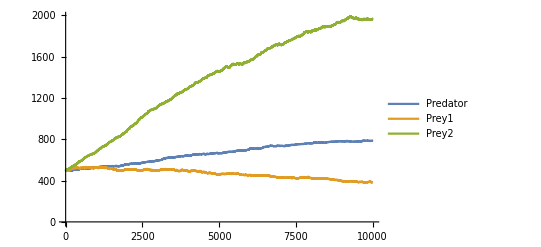

```mathematica
ListLinePlot[{historyPred, historyPrey1, historyPrey2}, PlotLegends-> {"Predator", "Prey1", "Prey2"}]
```

Population at end of evaluation

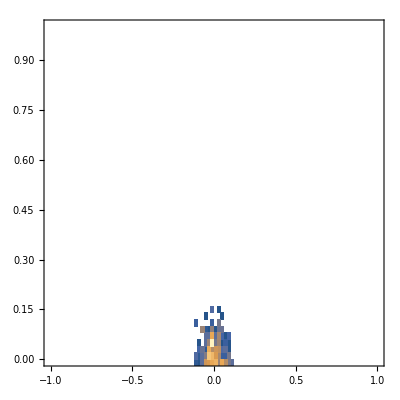

```mathematica
DensityHistogram[pop, PlotRange->{{-1,1},{0,1}}]
```